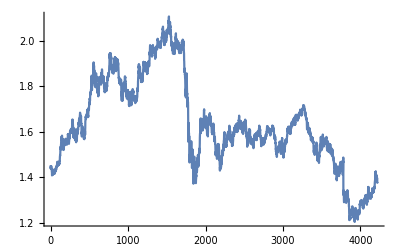

```mathematica
data=Import["/Users/wanghaibiao/Desktop/GBP USD 2002-2018.xlsx",{"Data",1,Table[i,{i,2,4220}],2}];
(*data import from 2002-01-02 to 2018-03-05*)
ListLinePlot[data]
(*plot the data, check the trend and whether it is a time series*)
```

```mathematica
(*we set the time line frim 0 to 4218, which is represent the trade date from 2002-01-02  to 2018-03-05. The data is changing by following time. And have trends in different time periods. However, the range of data change is a little bit large from around 1.2 to 2.2. We normally assume the financial data is exponential (we can find this from the trend of data), thus we decide to analyse the logarithmic data, not only make the range of data around 0 to 1, but also keep the same trends as the original data*)
```

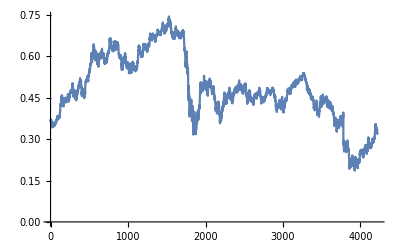

```mathematica
logdata=Log[data];(*take the ln data, two plots look similiar*)
ListLinePlot[Log[data]]
```

```mathematica
(*clearly, we can see the trends of data is random, there is no stable mean and volatility in different period of time, thus, the data is non-stationary*)
```

```mathematica
(*as for a non-stationary data, TimeSeriesModelFit will give the best seletion of the model based on the AIC value, ARIMA (0,1,0) is the random walk, base on the literature, random walk model has the "best" prediction power. Acturaly, the ARIMA(0,1,0) is the model, when the first difference of the data is follow the MA(0) process and AR(0) preocess*)
```

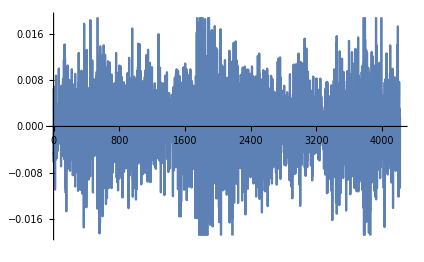

```mathematica
return=Differences[logdata];(*log return of the data, which is the first difference of the data*)
ListLinePlot[return]
```

```mathematica
For[n=1,n<14,n++,
For[j=0,j<21,j++,
t={252*(n-1)+j,756+252*(n-1)+j};
Subscript[return, n,j]=TimeSeries[Take[Drop[return,252*(n-1)+j],756],t];
Subscript[S, n,j]=TimeSeriesModelFit[Subscript[return, n,j]]];(*stationary model (NS)*)
(*set up rolling analysis, in general, we assume 252 trading days a year, then 3 years is 756 as a rolling window, and each window has one-year interval.*)


(*first find the best estimate model for the log return*)
Print["Period=",n,",",1];
Print[Normal[Subscript[S, n,1]]];
Print[Subscript[S, n,1]["CandidateSelectionTable"]];
Print[Subscript[S, n,1]["ParameterTable"]];
Print[];
Print[]]
```

Period=1,1

MAProcess[0.000353211,{-0.0555778},0.0000278859]

| Candidate | AIC
1 | MAProcess[1] | -7922.47
2 | ARProcess[1] | -7922.35
3 | MAProcess[0] | -7922.01
4 | MAProcess[2] | -7920.8
5 | ARMAProcess[1,1] | -7920.45
6 | ARMAProcess[1,2] | -7918.86

| Estimate | Standard Error | t-Statistic | P-Value
𝒷_1 | -0.0555778 | 0.0363134 | -1.5305 | 0.0631552

Period=2,1

MAProcess[0.000106924,{},0.0000314056]

| Candidate | AIC
1 | MAProcess[0] | -7834.6
2 | MAProcess[1] | -7832.89
3 | ARProcess[1] | -7832.89
4 | ARMAProcess[1,1] | -7830.92

Missing[NotAvailable]

Period=3,1

MAProcess[0.000117547,{},0.000030264]

| Candidate | AIC
1 | MAProcess[0] | -7862.6
2 | MAProcess[1] | -7860.62
3 | ARProcess[1] | -7860.62
4 | ARMAProcess[1,1] | -7858.63

Missing[NotAvailable]

Period=4,1

GARCHProcess[0.0000160248,{0.145192},{0.14683}]

| Candidate | AIC
1 | GARCHProcess[1,1] | -15546.9
2 | GARCHProcess[0,1] | -15542.3

| Estimate | Standard Error | t-Statistic | P-Value
α_1 | 0.145192 | 0.229302 | 0.633191 | 0.2634
β_1 | 0.14683 | 0.237154 | 0.619134 | 0.268007

Period=5,1

MAProcess[0.0000108438,{},0.0000262581]

| Candidate | AIC
1 | MAProcess[0] | -7969.94
2 | ARProcess[1] | -7969.9
3 | MAProcess[1] | -7969.57
4 | ARMAProcess[1,1] | -7967.79

Missing[NotAvailable]

Period=6,1

ARProcess[-0.000209146,{0.0833383},0.0000592007]

| Candidate | AIC
1 | ARProcess[1] | -7353.34
2 | MAProcess[1] | -7353.3
3 | ARProcess[2] | -7351.34
4 | ARMAProcess[1,1] | -7350.85
5 | MAProcess[0] | -7350.07
6 | ARMAProcess[2,1] | -7349.36

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 0.0833383 | 0.0362431 | 2.29942 | 0.0108763

Period=7,1

MAProcess[-0.000378579,{0.0603067},0.0000685598]

| Candidate | AIC
1 | MAProcess[1] | -7242.38
2 | ARProcess[1] | -7242.36
3 | MAProcess[0] | -7241.61
4 | MAProcess[2] | -7240.37
5 | ARMAProcess[1,1] | -7239.71
6 | ARMAProcess[1,2] | -7238.48

| Estimate | Standard Error | t-Statistic | P-Value
𝒷_1 | 0.0603067 | 0.0363035 | 1.66118 | 0.0485457

Period=8,1

MAProcess[-0.000099974,{0.0679225},0.0000653372]

| Candidate | AIC
1 | MAProcess[1] | -7278.78
2 | ARProcess[1] | -7278.6
3 | MAProcess[0] | -7277.1
4 | MAProcess[2] | -7277.03
5 | ARMAProcess[1,1] | -7275.29
6 | ARMAProcess[1,2] | -7274.99

| Estimate | Standard Error | t-Statistic | P-Value
𝒷_1 | 0.0679225 | 0.0362857 | 1.87188 | 0.0308043

Period=9,1

MAProcess[-0.0000307408,{-0.0509518},0.0000316889]

| Candidate | AIC
1 | MAProcess[1] | -7825.82
2 | MAProcess[0] | -7825.7
3 | ARProcess[1] | -7825.66
4 | MAProcess[2] | -7824.94
5 | ARMAProcess[1,1] | -7824.22
6 | ARMAProcess[1,2] | -7822.75

| Estimate | Standard Error | t-Statistic | P-Value
𝒷_1 | -0.0509518 | 0.0363224 | -1.40277 | 0.0805486

Period=10,1

MAProcess[-6.62×10^-6,{},0.0000235607]

| Candidate | AIC
1 | MAProcess[0] | -8051.88
2 | MAProcess[1] | -8051.32
3 | ARProcess[1] | -8051.23
4 | ARMAProcess[1,1] | -8049.29

Missing[NotAvailable]

Period=11,1

MAProcess[0.0000593297,{},0.0000180108]

| Candidate | AIC
1 | MAProcess[0] | -8254.95
2 | MAProcess[1] | -8252.97
3 | ARProcess[1] | -8252.97
4 | ARMAProcess[1,1] | -8250.89

Missing[NotAvailable]

Period=12,1

GARCHProcess[0.0000136004,{0.147424},{0.146911}]

| Candidate | AIC
1 | GARCHProcess[1,1] | -15581.7
2 | GARCHProcess[0,1] | -15560.8

| Estimate | Standard Error | t-Statistic | P-Value
α_1 | 0.147424 | 0.225577 | 0.653544 | 0.256802
β_1 | 0.146911 | 0.233472 | 0.629246 | 0.264689

Period=13,1

GARCHProcess[0.0000264179,{0.106821},{0.14684}]

| Candidate | AIC
1 | GARCHProcess[1,1] | -12209.2
2 | GARCHProcess[0,1] | -12206.3

| Estimate | Standard Error | t-Statistic | P-Value
α_1 | 0.106821 | 0.317071 | 0.336899 | 0.368143
β_1 | 0.14684 | 0.324239 | 0.452876 | 0.325384

```mathematica
(*we can see, most period use MA(0) process as the best fit*)
```

```mathematica
For[n=1,n<14,n++,
For[j=0,j<21,j++,
t={252*(n-1)+j,756+252*(n-1)+j};
Subscript[return, n,j]=TimeSeries[Take[Drop[return,252*(n-1)+j],756],t];
Subscript[logdata, n,j]=TimeSeries[Take[Drop[logdata,252*(n-1)+j],756],t];
(*set up rolling analysis, in general, we assume 252 trading days a year, then 3 years is 756 as a rolling window, and each window has one-year interval.*)]]
```

Period n=1

MA(0) model

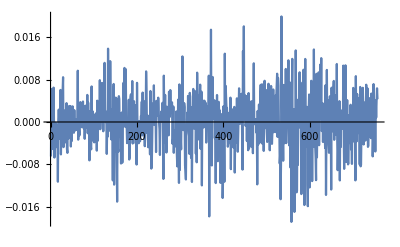

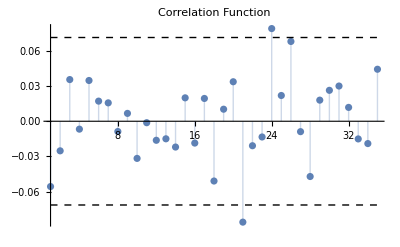

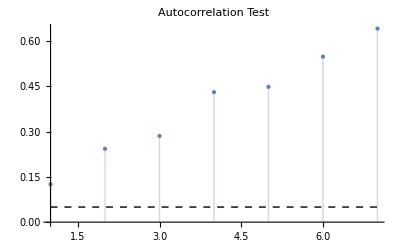

ARIMA(0,1,0) model

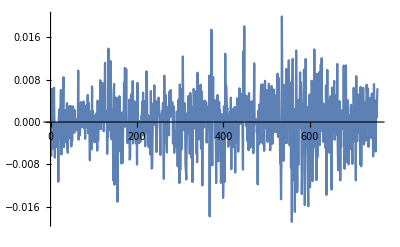

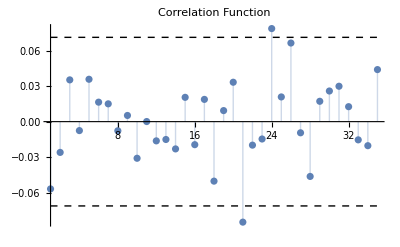

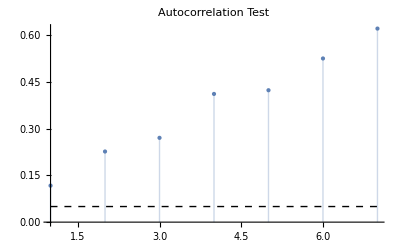

Period n=2

MA(0) model

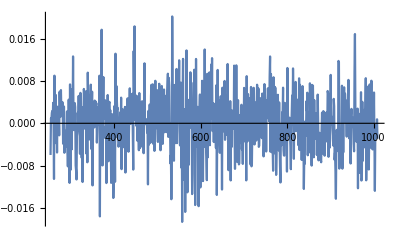

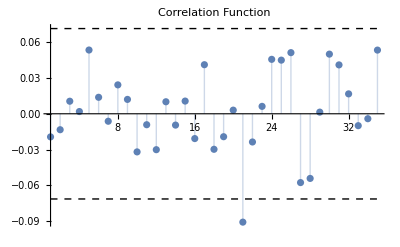

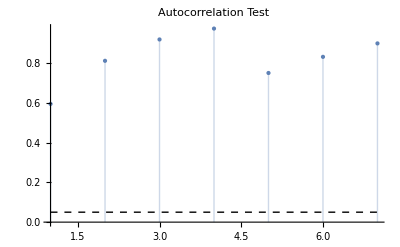

ARIMA(0,1,0) model

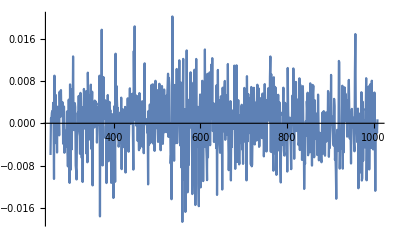

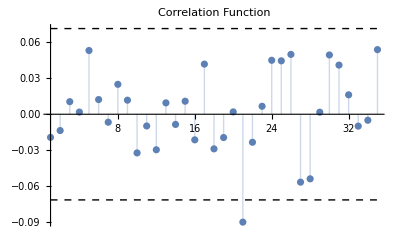

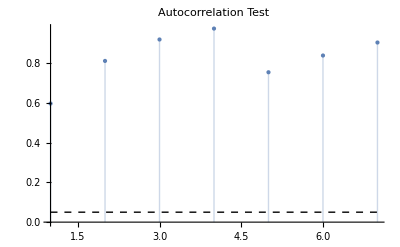

Period n=3

MA(0) model

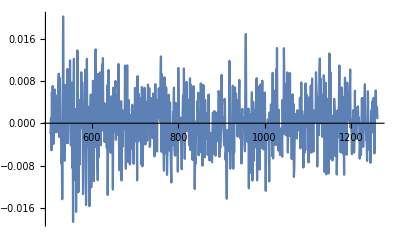

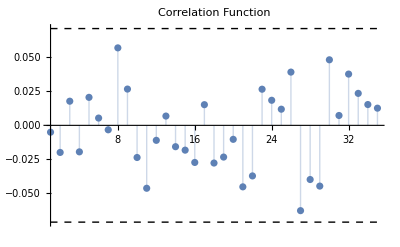

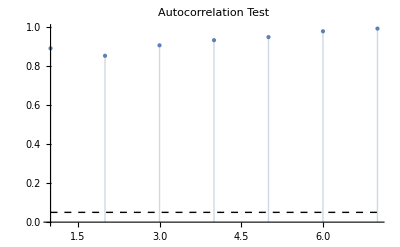

ARIMA(0,1,0) model

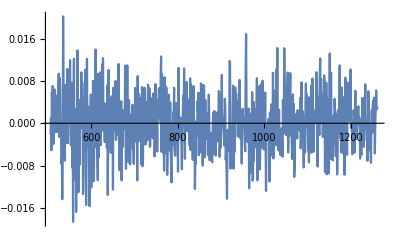

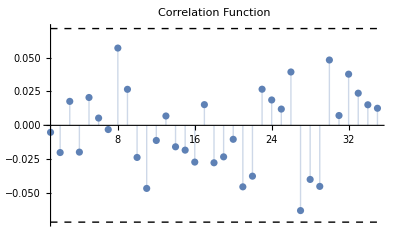

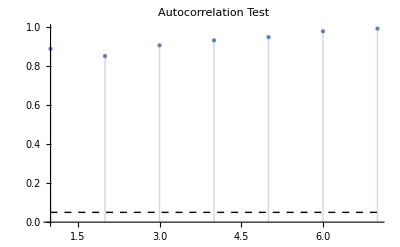

Period n=4

MA(0) model

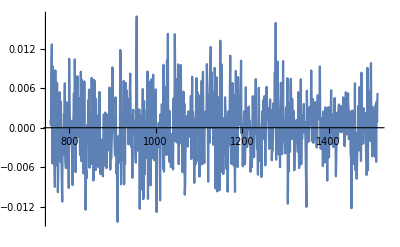

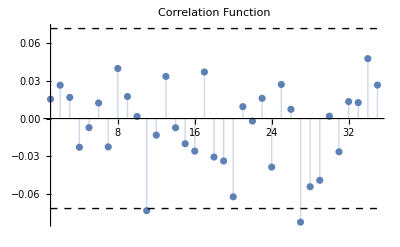

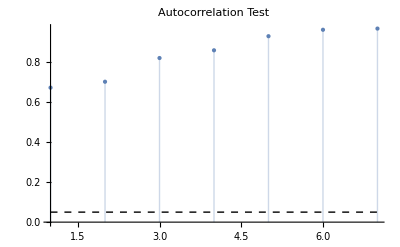

ARIMA(0,1,0) model

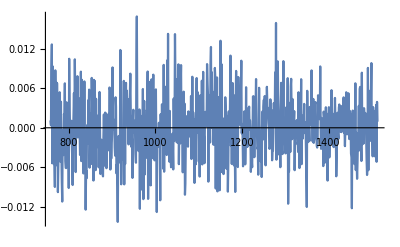

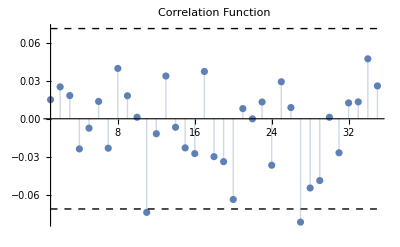

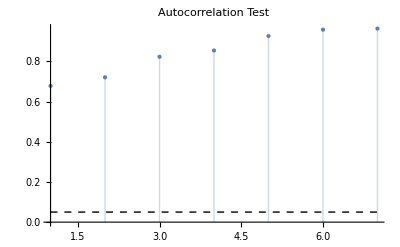

Period n=5

MA(0) model

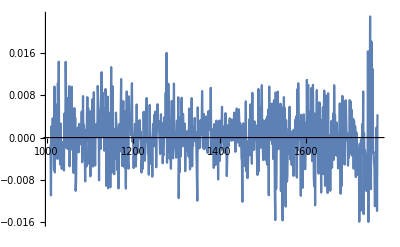

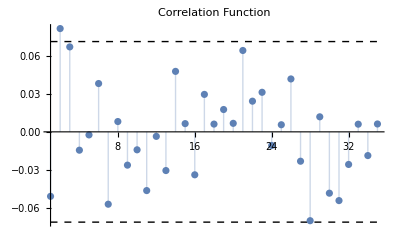

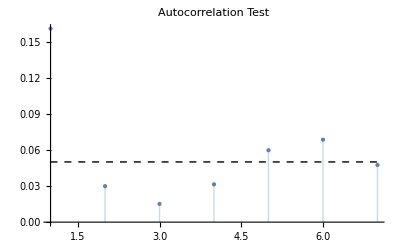

ARIMA(0,1,0) model

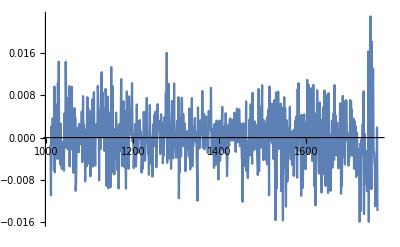

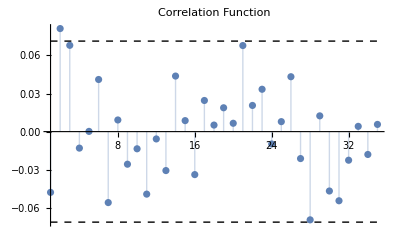

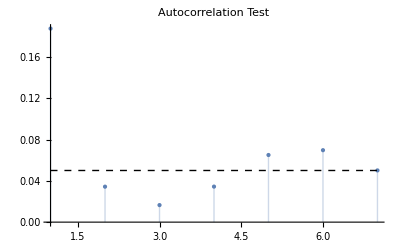

Period n=6

MA(0) model

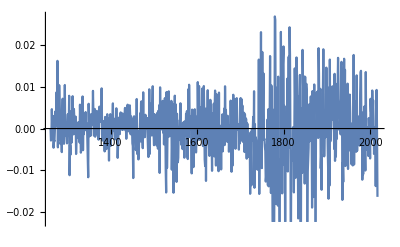

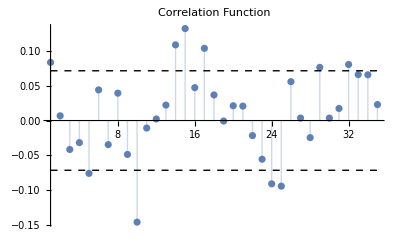

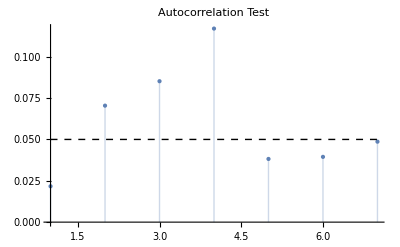

ARIMA(0,1,0) model

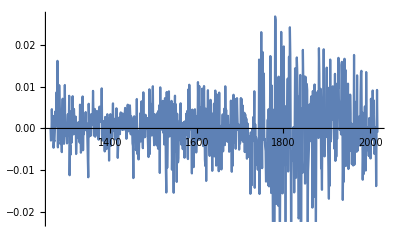

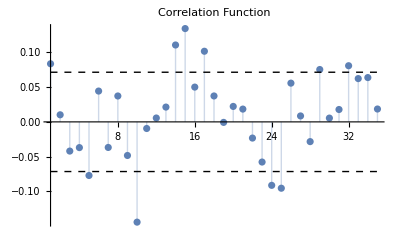

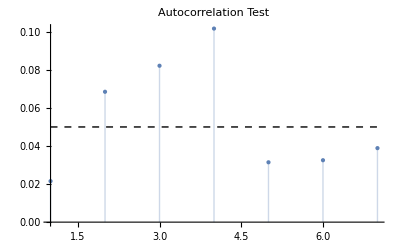

Period n=7

MA(0) model

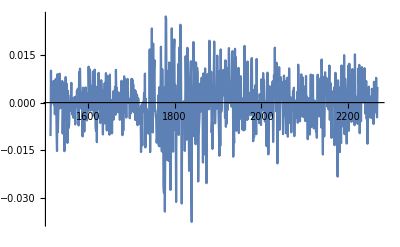

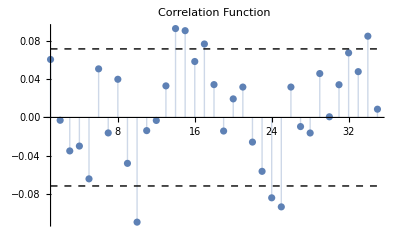

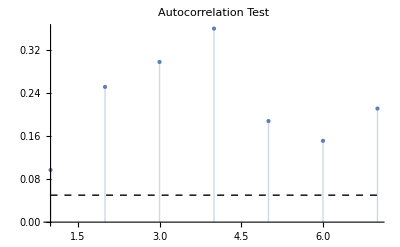

ARIMA(0,1,0) model

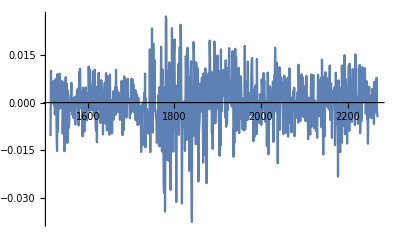

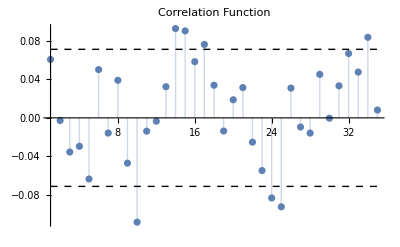

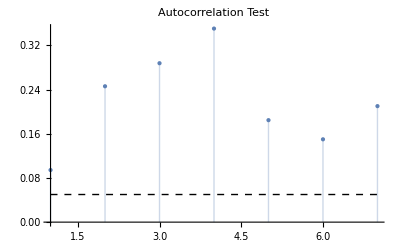

Period n=8

MA(0) model

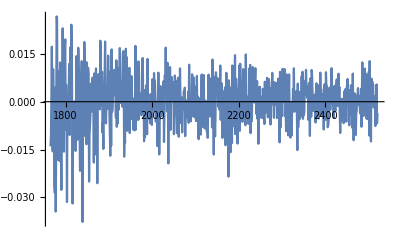

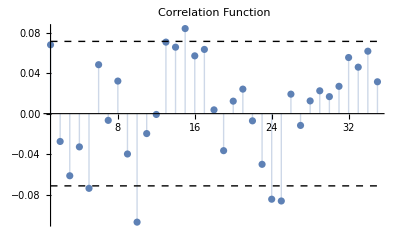

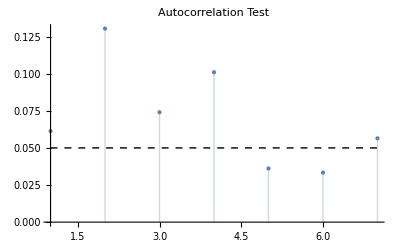

ARIMA(0,1,0) model

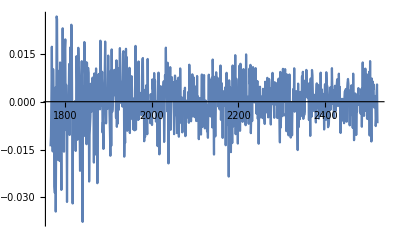

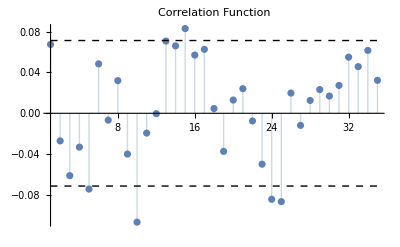

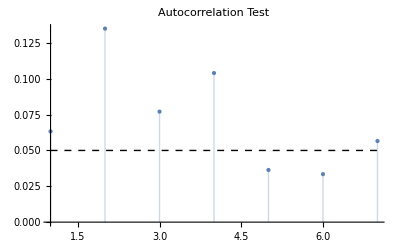

Period n=9

MA(0) model

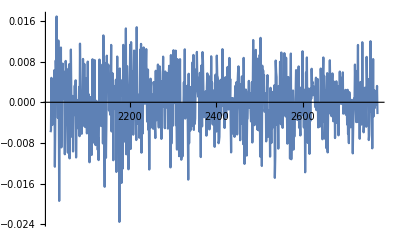

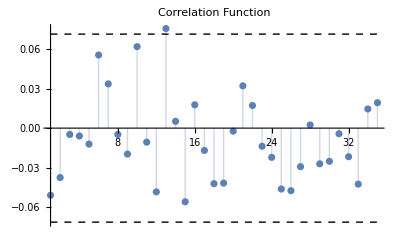

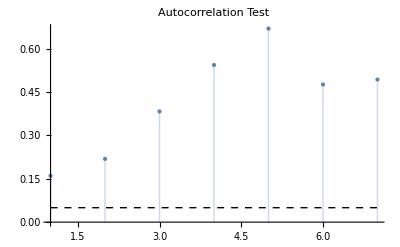

ARIMA(0,1,0) model

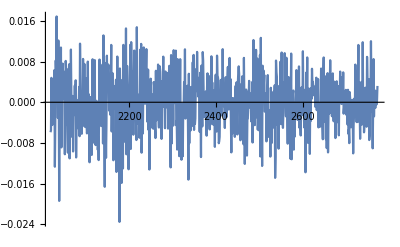

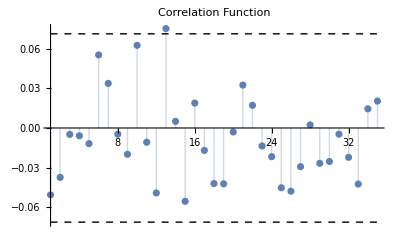

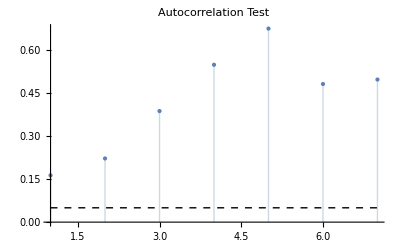

Period n=10

MA(0) model

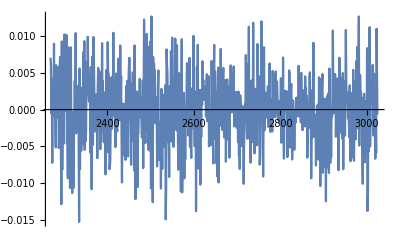

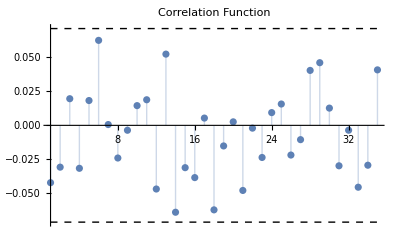

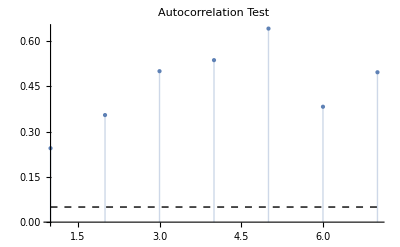

ARIMA(0,1,0) model

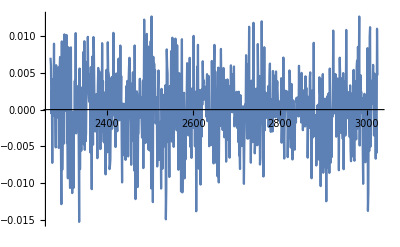

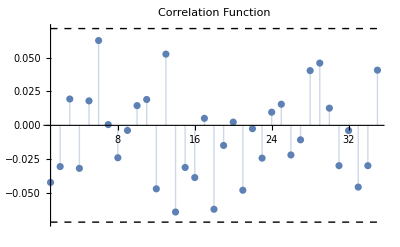

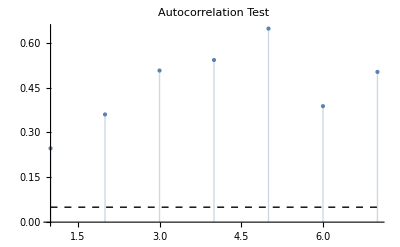

Period n=11

MA(0) model

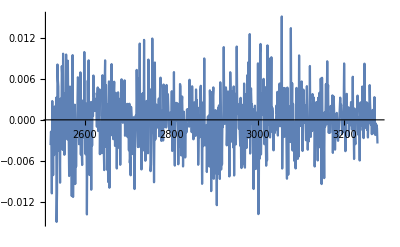

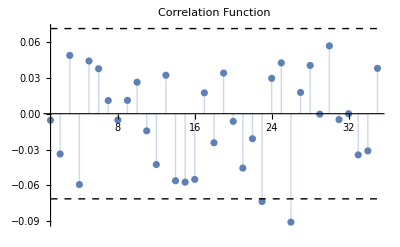

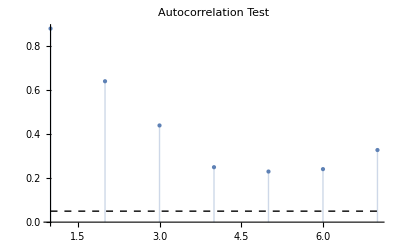

ARIMA(0,1,0) model

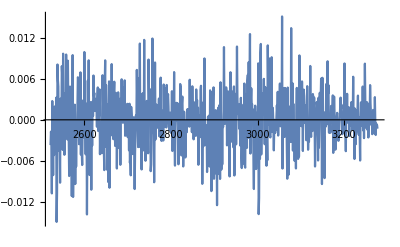

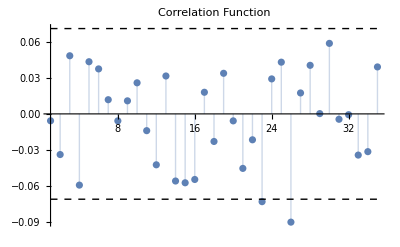

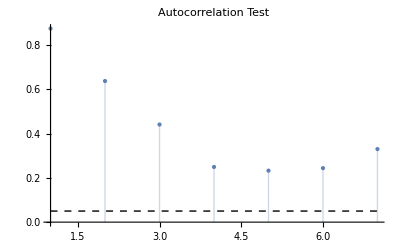

Period n=12

MA(0) model

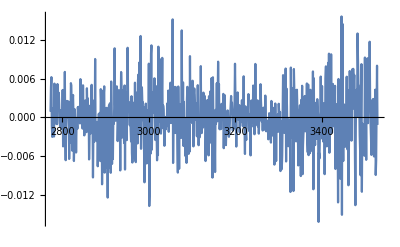

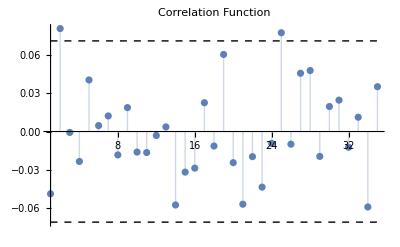

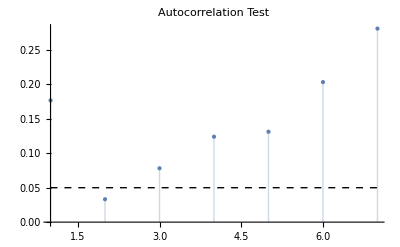

ARIMA(0,1,0) model

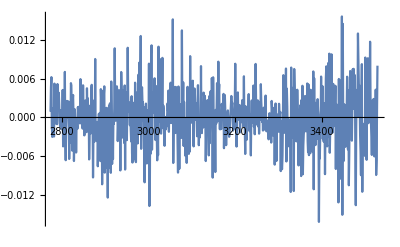

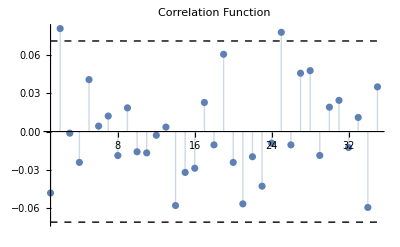

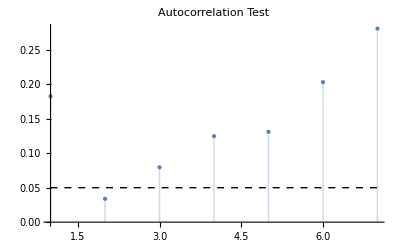

Period n=13

MA(0) model

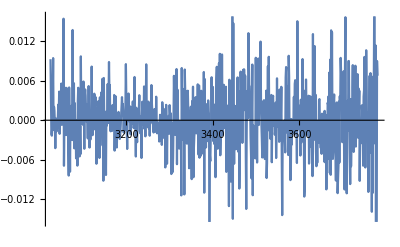

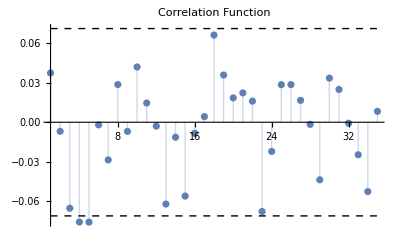

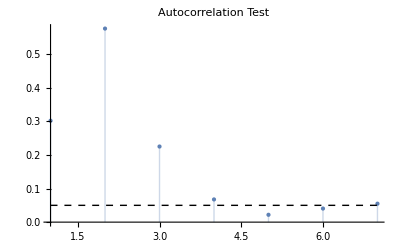

ARIMA(0,1,0) model

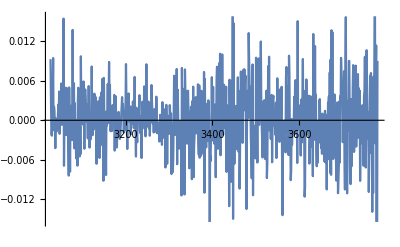

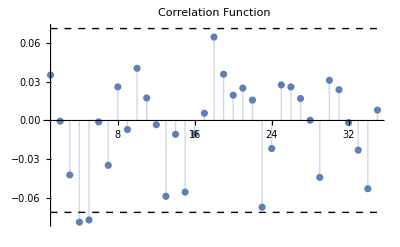

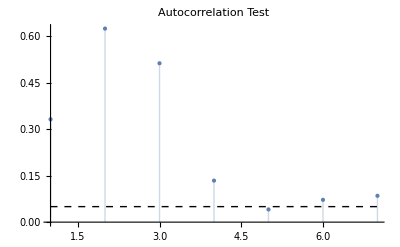

```mathematica
For[n=1,n<14,n++,
For[j=0,j<21,j++,
Subscript[model1, n,j]=TimeSeriesModelFit[Subscript[return, n,j],{"MA",{0}}];
(*use the MA(0) estimate each period*)
Subscript[model2, n,j]=TimeSeriesModelFit[Subscript[logdata, n,j],{"ARIMA",{0,1,0}}];
(*Use ARIMA(0,1,0) as the random walk process, which is Subscript[X, t]=u+Subscript[X, t-1]+Subscript[e, t], to fit each period.If the series X is not stationary,the simplest possible model for it is a random walk model,which can be considered as a limiting case of an AR(1) model in which the autoregressive coefficient is equal to 1,i.e.,a series with infinitely slow mean reversion.The prediction equation for this model can be written as: 
hat Subscript[(X), t]=u+Subscript[X, t-1]*)
Subscript[forecast1, n,j]=TimeSeriesForecast[Subscript[model1, n,j],1];
Subscript[forecast2, n,j]=TimeSeriesForecast[Subscript[model2, n,j],1];
Subscript[forecast1, n]=TimeSeries[{Subscript[forecast1, n,0],Subscript[forecast1, n,1],Subscript[forecast1, n,2],Subscript[forecast1, n,3],Subscript[forecast1, n,4],Subscript[forecast1, n,5],Subscript[forecast1, n,6],Subscript[forecast1, n,7],Subscript[forecast1, n,8],Subscript[forecast1, n,9],Subscript[forecast1, n,10],Subscript[forecast1, n,11],Subscript[forecast1, n,12],Subscript[forecast1, n,13],Subscript[forecast1, n,14],Subscript[forecast1, n,15],Subscript[forecast1, n,16],Subscript[forecast1, n,17],Subscript[forecast1, n,18],Subscript[forecast1, n,19],Subscript[forecast1, n,20]},{757+252*(n-1),777+252*(n-1)}];
Subscript[forecast2, n]=TimeSeries[{Subscript[forecast2, n,0],Subscript[forecast2, n,1],Subscript[forecast2, n,2],Subscript[forecast2, n,3],Subscript[forecast2, n,4],Subscript[forecast2, n,5],Subscript[forecast2, n,6],Subscript[forecast2, n,7],Subscript[forecast2, n,8],Subscript[forecast2, n,9],Subscript[forecast2, n,10],Subscript[forecast2, n,11],Subscript[forecast2, n,12],Subscript[forecast2, n,13],Subscript[forecast2, n,14],Subscript[forecast2, n,15],Subscript[forecast2, n,16],Subscript[forecast2, n,17],Subscript[forecast2, n,18],Subscript[forecast2, n,19],Subscript[forecast2, n,20]},{757+252*(n-1),777+252*(n-1)}]];
Print["Period n=",n];
Print["MA(0) model"];
Print[ListLinePlot[Subscript[model1, n,1]["FitResiduals"]]];
Print[Subscript[model1, n,1]["ACFPlot"]];
Print[Subscript[model1, n,1]["LjungBoxPlot"]];
Print["ARIMA(0,1,0) model"];
Print[ListLinePlot[Subscript[model2, n,1]["FitResiduals"]]];
Print[Subscript[model2, n,1]["ACFPlot"]];
Print[Subscript[model2, n,1]["LjungBoxPlot"]]]
```

Period=1

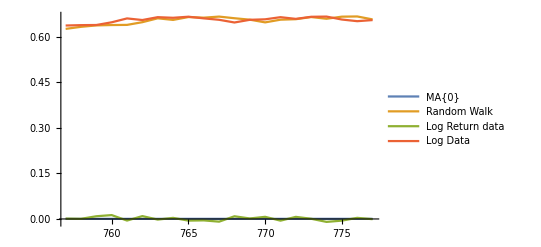

Period=2

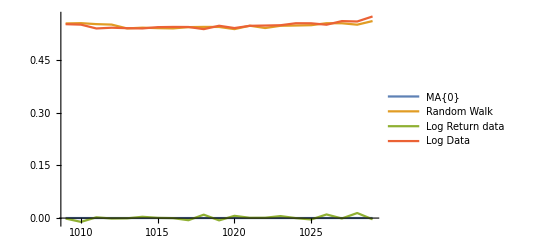

Period=3

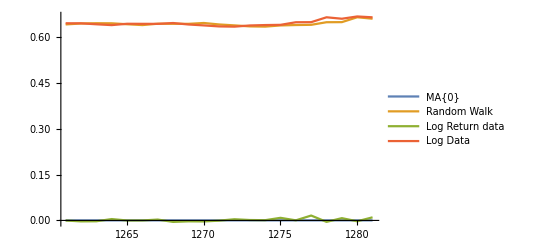

Period=4

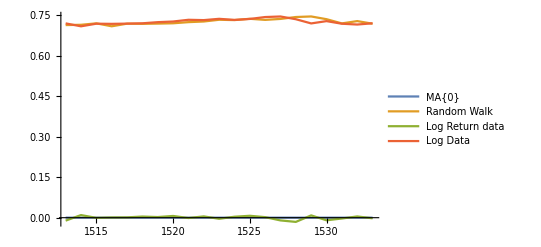

Period=5

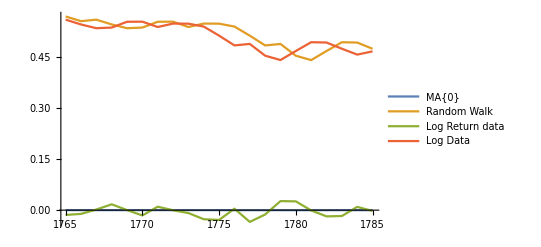

Period=6

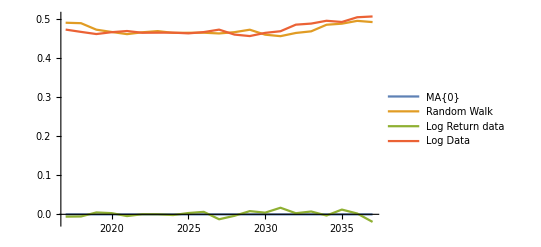

Period=7

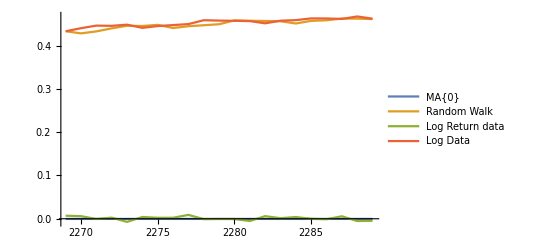

Period=8

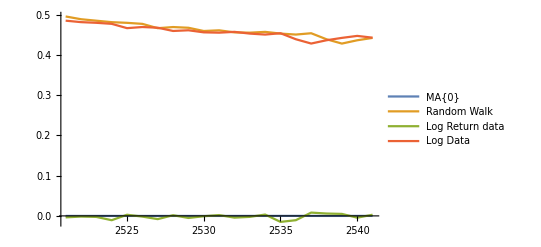

Period=9

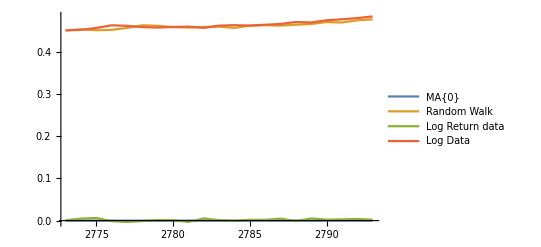

Period=10

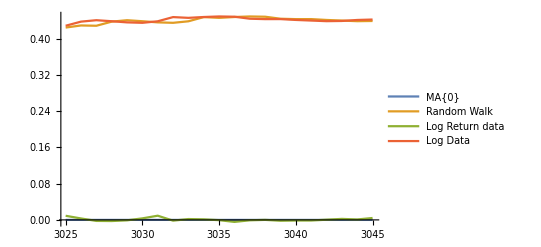

Period=11

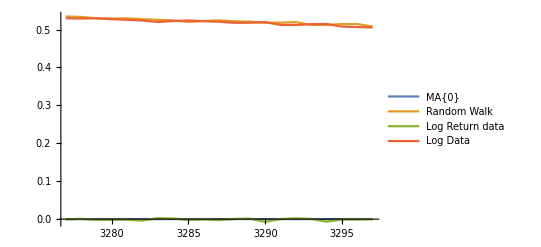

Period=12

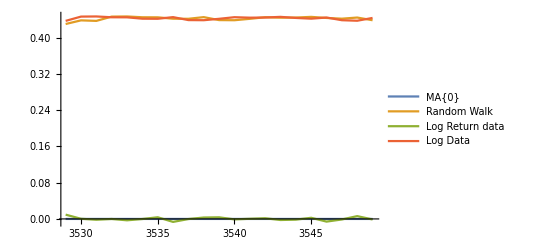

Period=13

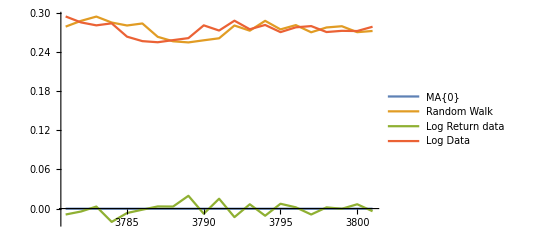

```mathematica
For[n=1,n<14,n++,
k={757+252*(n-1),777+252*(n-1)};
Subscript[predictionpart1, n]=TimeSeries[Take[Drop[return,757+252*(n-1)],21],k]; 
Subscript[predictionpart2, n]=TimeSeries[Take[Drop[logdata,757+252*(n-1)],21],k]; 
(*take the 21-step real values, in order to compare with the direction changes of two models*)
Print["Period=",n];
Print[ListLinePlot[{Subscript[forecast3, n],Subscript[forecast2, n],Subscript[predictionpart1, n],Subscript[predictionpart2, n]},PlotLegends->{"MA{0}","Random Walk","Log Return data","Log Data"}]]]
```

Period n=1

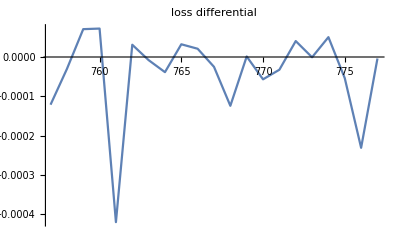

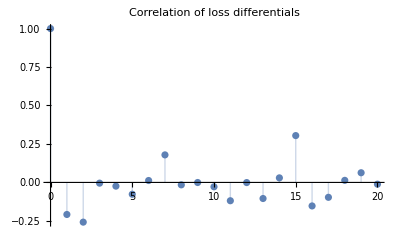

Period n=2

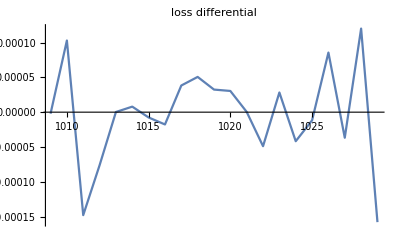

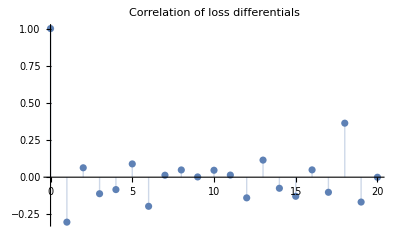

Period n=3

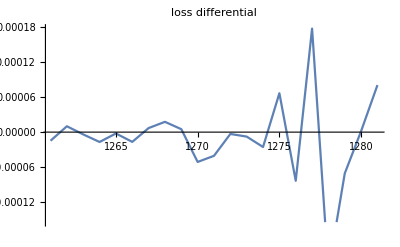

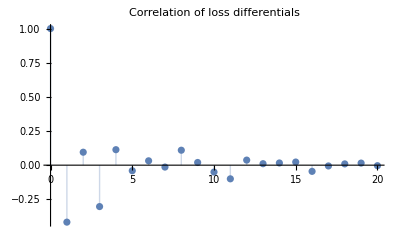

Period n=4

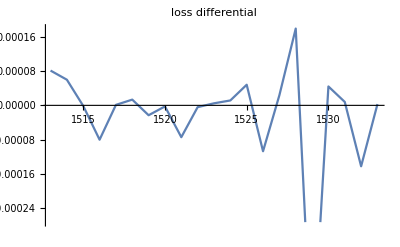

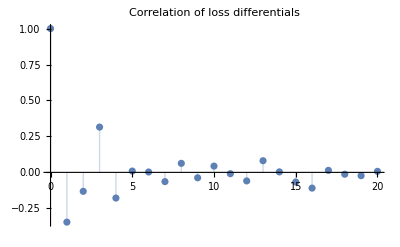

Period n=5

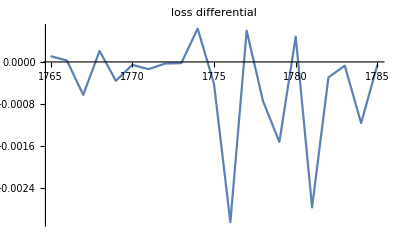

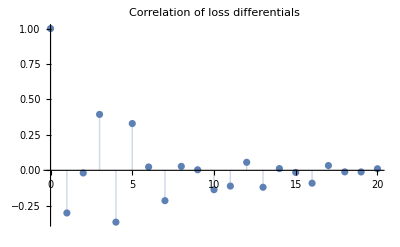

Period n=6

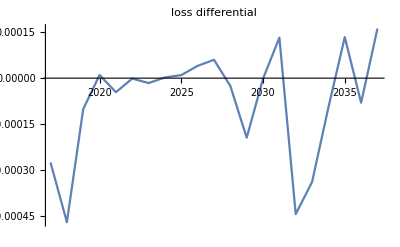

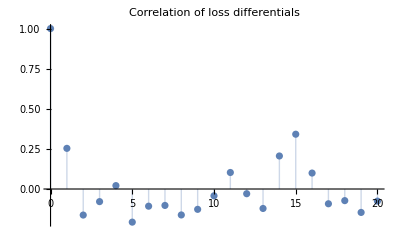

Period n=7

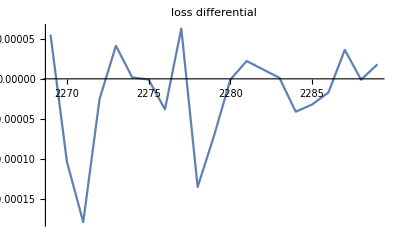

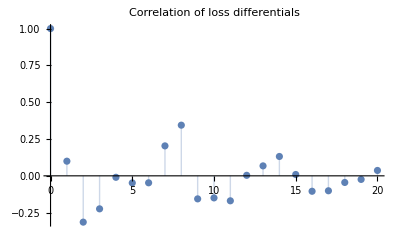

Period n=8

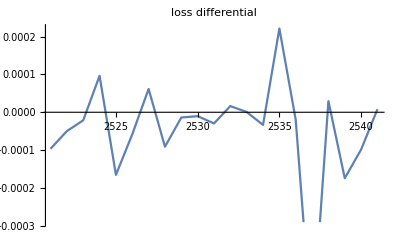

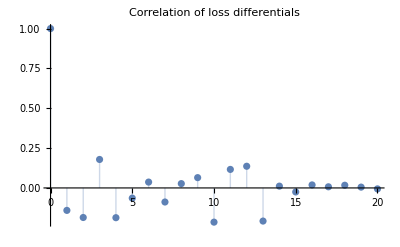

Period n=9

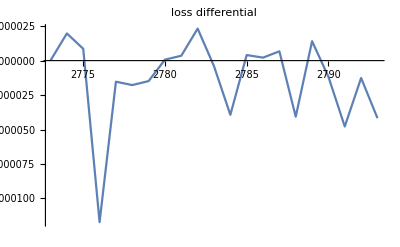

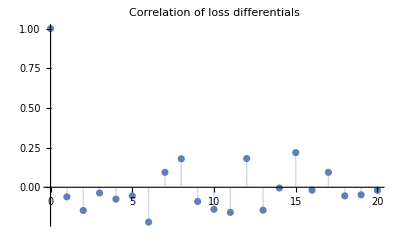

Period n=10

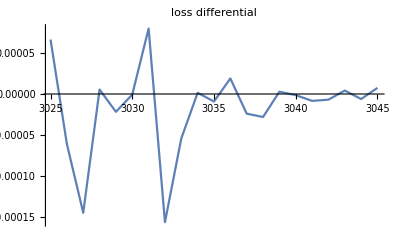

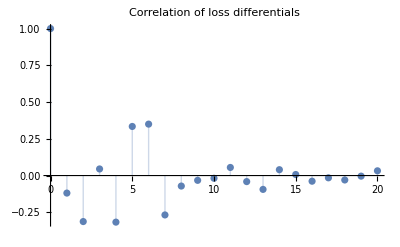

Period n=11

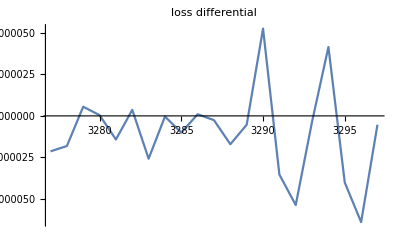

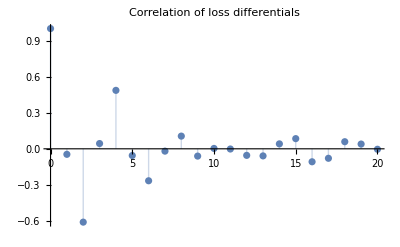

Period n=12

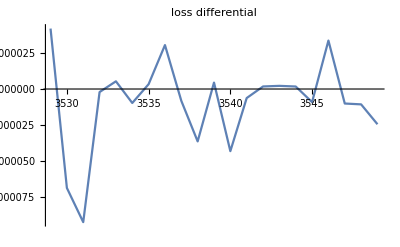

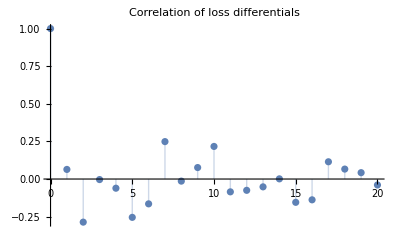

Period n=13

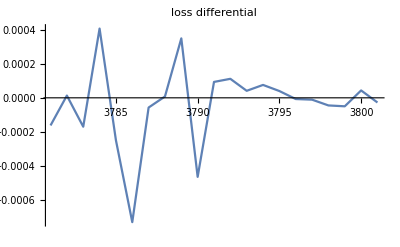

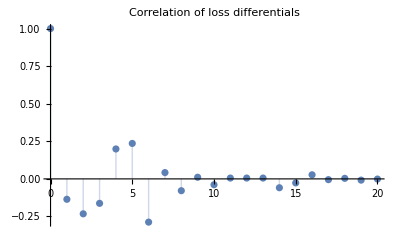

```mathematica
For[n=1,n<14,n++,
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[predictionpart1, n];(*forecast error of model 3*)
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[predictionpart2, n];(*forecast error of model 2*)
Subscript[d, n]=Subscript[forecasterror1, n]^2 - Subscript[forecasterror2, n]^2;(*loss differential is equal to differences between two quadratic losses*)
(*Before we start the Direbold Mariano Test, we should check the loss differential, this time series, is satisfy covariance stationary, which is the main assumption of the DM Test*)
Print["Period n=",n];
Print[ListLinePlot[Subscript[d, n],PlotLabel->"loss differential"]];
Print[ListPlot[CorrelationFunction[Subscript[d, n],{20}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]];
Print[]]
```

```mathematica
For[n=1,n<14,n++,
For [j=1,j≤21,j++,
Subscript[d, n,j]=Subscript[d, n]["Values"][[j]]];(*each element of Subscript[d, n]*)
Subscript[f, n,d]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/20]≤1],1/21,Sum[Times[Subscript[d, n,j]-Mean[Subscript[d, n]],Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]],{j,Abs[tau]+1,21}]],{tau,-20,20}];(*we use Subscript[f, d] instead of Subscript[f, d](0), which is the spectral density of the loss differential at frequency zero, where Subscript[f, d](0)=(1/(2*Pi))*Sum[Boole[Abs[tau/20]≤1]*(1/21)*Subscript[gamma, d](tau),{tau,-20,20}],

and Subscript[gamma, d](tau)=Sum[(Subscript[d, n,j]-Mean[Subscript[d, n]])*(Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]),{j,Abs[tau]+1,21}]
, which is the autocovariance of the loss differential at displacement tau,

Boole[Abs[tau/S(T)]≤1] is is the lag window,and S(T) is the truncation lag, in this case, S(T)=20, since  it is 21-step ahead, recall the familiar result that optimal k-step-ahead forecast errors are at most (k-1)-dependent, thus, S(T)=20*)
Subscript[S, n]=Divide[Mean[Subscript[d, n]],Sqrt[(2*Pi*Subscript[f, n,d])/21]];
Print["Period=",n];
Print[If[Subscript[f, n,d]<=0,"f_(n, d) <=0,"False,{Subscript[S, n],TrueQ[-1.96<=Subscript[S, n]<=1.96]}]];
(*Because the Dirichlet spectral window associated with the rectangular lag window dips below zero at certain locations,the resulting estimator of the spectral density function is not guaranteed to be positive semi-definite.The large positive weight near the origin associated with the Dirichlet kernel,however,makes it unlikely to obtain a negative estimate of fd(0).In applications,in the rare event that a negative estimate arises,we treat it as zero and automatically reject the null hypothesis of equal forecast accuracy.*)
Print[]]
```

Period=1

f_(n, d) <=0, False

Period=2

{-1.26464×10^7,False}

Period=3

f_(n, d) <=0, False

Period=4

f_(n, d) <=0, False

Period=5

{-1.94995×10^8,False}

Period=6

{-2.13474×10^8,False}

Period=7

f_(n, d) <=0, False

Period=8

f_(n, d) <=0, False

Period=9

{-1.70004×10^8,False}

Period=10

f_(n, d) <=0, False

Period=11

{-1.24707×10^8,False}

Period=12

f_(n, d) <=0, False

Period=13

{-4.01785×10^7,False}

```mathematica
For[n=1,n<14,n++,
For[j=0,j<21,j++,
Subscript[model3, n,j]=TimeSeriesModelFit[Subscript[return, n,j],{"MA",{0}}];
(*use the MA(0) estimate each period*)
Subscript[model2, n,j]=TimeSeriesModelFit[Subscript[logdata, n,j],{"ARIMA",{0,1,0}}];
(*Use ARIMA(0,1,0) as the random walk process, which is Subscript[X, t]=u+Subscript[X, t-1]+Subscript[e, t], to fit each period.If the series X is not stationary,the simplest possible model for it is a random walk model,which can be considered as a limiting case of an AR(1) model in which the autoregressive coefficient is equal to 1,i.e.,a series with infinitely slow mean reversion.The prediction equation for this model can be written as: 
hat Subscript[(X), t]=u+Subscript[X, t-1]*)
Subscript[forecast3, n,j]=TimeSeriesForecast[Subscript[model3, n,j],21];
Subscript[forecast2, n,j]=TimeSeriesForecast[Subscript[model2, n,j],21];
Subscript[forecast3, n]=TimeSeries[{Subscript[forecast3, n,0],Subscript[forecast3, n,1],Subscript[forecast3, n,2],Subscript[forecast3, n,3],Subscript[forecast3, n,4],Subscript[forecast3, n,5],Subscript[forecast3, n,6],Subscript[forecast3, n,7],Subscript[forecast3, n,8],Subscript[forecast3, n,9],Subscript[forecast3, n,10],Subscript[forecast3, n,11],Subscript[forecast3, n,12],Subscript[forecast3, n,13],Subscript[forecast3, n,14],Subscript[forecast3, n,15],Subscript[forecast3, n,16],Subscript[forecast3, n,17],Subscript[forecast3, n,18],Subscript[forecast3, n,19],Subscript[forecast3, n,20]},{777+252*(n-1),797+252*(n-1)}];
Subscript[forecast4, n]=TimeSeries[{Subscript[forecast2, n,0],Subscript[forecast2, n,1],Subscript[forecast2, n,2],Subscript[forecast2, n,3],Subscript[forecast2, n,4],Subscript[forecast2, n,5],Subscript[forecast2, n,6],Subscript[forecast2, n,7],Subscript[forecast2, n,8],Subscript[forecast2, n,9],Subscript[forecast2, n,10],Subscript[forecast2, n,11],Subscript[forecast2, n,12],Subscript[forecast2, n,13],Subscript[forecast2, n,14],Subscript[forecast2, n,15],Subscript[forecast2, n,16],Subscript[forecast2, n,17],Subscript[forecast2, n,18],Subscript[forecast2, n,19],Subscript[forecast2, n,20]},{777+252*(n-1),797+252*(n-1)}]]]
```

Period=1

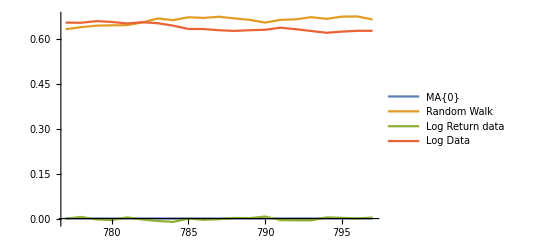

Period=2

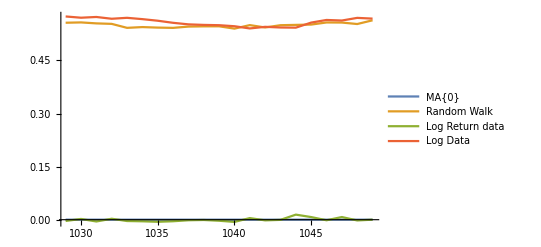

Period=3

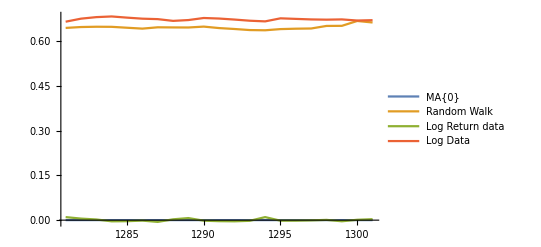

Period=4

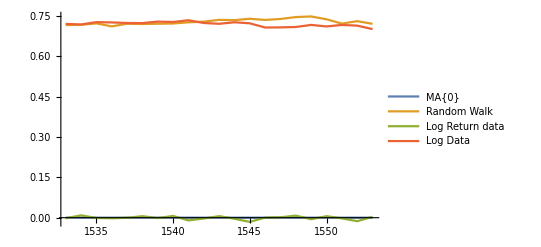

Period=5

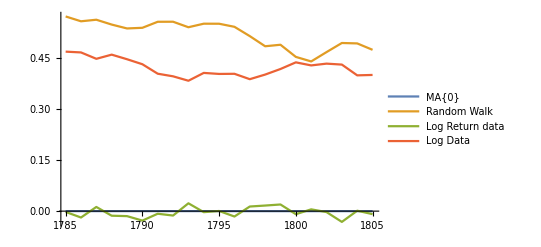

Period=6

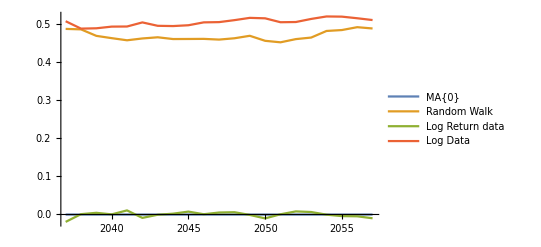

Period=7

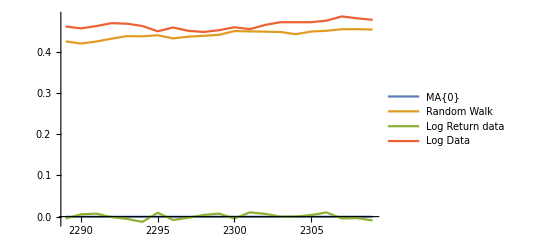

Period=8

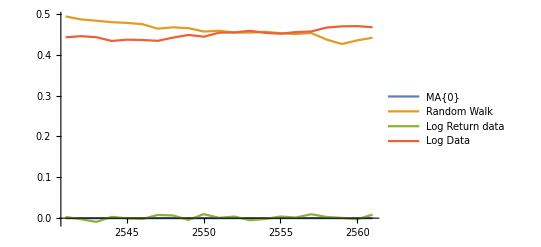

Period=9

-Graphics-

Period=10

-Graphics-

Period=11

-Graphics-

Period=12

-Graphics-

Period=13

-Graphics-

```mathematica
For[n=1,n<14,n++,
k={777+252*(n-1),797+252*(n-1)};
Subscript[predictionpart3, n]=TimeSeries[Take[Drop[return,777+252*(n-1)],21],k]; 
Subscript[predictionpart4, n]=TimeSeries[Take[Drop[logdata,777+252*(n-1)],21],k]; 
(*take the 21-step real values, in order to compare with the direction changes of two models*)
Print["Period=",n];
Print[ListLinePlot[{Subscript[forecast3, n],Subscript[forecast4, n],Subscript[predictionpart3, n],Subscript[predictionpart4, n]},PlotLegends->{"MA{0}","Random Walk","Log Return data","Log Data"}]]]
```

```mathematica
For[n=1,n<14,n++,
Subscript[forecasterror3, n]=Subscript[forecast3, n]-Subscript[predictionpart3, n];(*forecast error of model 3*)
Subscript[forecasterror4, n]=Subscript[forecast4, n]-Subscript[predictionpart4, n];(*forecast error of model 2*)
Subscript[d, n]=Subscript[forecasterror3, n]^2 - Subscript[forecasterror4, n]^2;(*loss differential is equal to differences between two quadratic losses*)
(*Before we start the Direbold Mariano Test, we should check the loss differential, this time series, is satisfy covariance stationary, which is the main assumption of the DM Test*)
Print[ListLinePlot[Subscript[d, n],PlotLabel->"loss differential"]];
Print[ListPlot[CorrelationFunction[Subscript[d, n],{20}],PlotLabel->"Correlations of loss differential",Filling->Axis,PlotRange->All]];
For[j=1,j<=20,j++,
Subscript[d, n,j]=Subscript[d, n]["Values"][[j]]];(*each element of Subscript[d, n]*)
Subscript[f, n,d]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/20]≤1],1/21,Sum[Times[Subscript[d, n,j]-Mean[Subscript[d, n]],Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]],{j,Abs[tau]+1,21}]],{tau,-20,20}];(*we use Subscript[f, d] instead of Subscript[f, d](0), which is the spectral density of the loss differential at frequency zero, where Subscript[f, d](0)=(1/(2*Pi))*Sum[Boole[Abs[tau/20]≤1]*(1/21)*Subscript[gamma, d](tau),{tau,-20,20}],

and Subscript[gamma, d](tau)=Sum[(Subscript[d, n,j]-Mean[Subscript[d, n]])*(Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]),{j,Abs[tau]+1,21}]
, which is the autocovariance of the loss differential at displacement tau,

Boole[Abs[tau/S(T)]≤1] is is the lag window,and S(T) is the truncation lag, in this case, S(T)=20, since  it is 21-step ahead, recall the familiar result that optimal k-step-ahead forecast errors are at most (k-1)-dependent, thus, S(T)=20*)
Subscript[S, n]=Divide[Mean[Subscript[d, n]],Sqrt[(2*Pi*Subscript[f, n,d])/21]];
Print["Period=",n];
Print[If[Subscript[f, n,d]<=0,"f_(n, d) <=0,"False,{Subscript[S, n],TrueQ[-1.96<=Subscript[S, n]<=1.96]}]];
(*Because the Dirichlet spectral window associated with the rectangular lag window dips below zero at certain locations,the resulting estimator of the spectral density function is not guaranteed to be positive semi-definite.The large positive weight near the origin associated with the Dirichlet kernel,however,makes it unlikely to obtain a negative estimate of fd(0).In applications,in the rare event that a negative estimate arises,we treat it as zero and automatically reject the null hypothesis of equal forecast accuracy.*)
Print[]]
```

-Graphics-

-Graphics-

Period=1

{-15.428,False}

-Graphics-

-Graphics-

Period=2

{-23.0595,False}

-Graphics-

-Graphics-

Period=3

{-122.892,False}

-Graphics-

-Graphics-

Period=4

{-14.7687,False}

-Graphics-

-Graphics-

Period=5

{-44.7999,False}

-Graphics-

-Graphics-

Period=6

{-53.856,False}

-Graphics-

-Graphics-

Period=7

{-25.0286,False}

-Graphics-

-Graphics-

Period=8

{-29.393,False}

-Graphics-

-Graphics-

Period=9

{-249.151,False}

-Graphics-

-Graphics-

Period=10

{-7.33062,False}

-Graphics-

-Graphics-

Period=11

{-115.174,False}

-Graphics-

-Graphics-

Period=12

{-27.6669,False}

-Graphics-

-Graphics-

Period=13

{-20.4171,False}

```mathematica
For[n=1,n<14,n++,
For[k=0,k<63,k++,
t={252*(n-1)+k,756+252*(n-1)+k};
Subscript[return, n,k]=TimeSeries[Take[Drop[return,252*(n-1)+k],756],t];
Subscript[logdata, n,k]=TimeSeries[Take[Drop[logdata,252*(n-1)+k],756],t];
(*set up rolling analysis, in general, we assume 252 trading days a year, then 3 years is 756 as a rolling window, and each window has one-year interval.*)
Subscript[model8, n,k]=TimeSeriesModelFit[Subscript[return, n,k],{"MA",{0}}];
(*use the MA(0) estimate each period*)
Subscript[model9, n,k]=TimeSeriesModelFit[Subscript[logdata, n,k],{"ARIMA",{0,1,0}}]]]
(*Use ARIMA(0,1,0) as the random walk process, which is Subscript[X, t]=u+Subscript[X, t-1]+Subscript[e, t], to fit each period.If the series X is not stationary,the simplest possible model for it is a random walk model,which can be considered as a limiting case of an AR(1) model in which the autoregressive coefficient is equal to 1,i.e.,a series with infinitely slow mean reversion.The prediction equation for this model can be written as: 
hat Subscript[(X), t]=u+Subscript[X, t-1]*)
```

```mathematica
For[n=1,n<14,n++,
For[k=0,k<63,k++,
Subscript[forecast8, n,k]=TimeSeriesForecast[Subscript[model8, n,k],1];
Subscript[forecast9, n,k]=TimeSeriesForecast[Subscript[model9, n,k],1]];
Subscript[forecast8, n]=TimeSeries[{Subscript[forecast8, n,0],Subscript[forecast8, n,1],Subscript[forecast8, n,2],Subscript[forecast8, n,3],Subscript[forecast8, n,4],Subscript[forecast8, n,5],Subscript[forecast8, n,6],Subscript[forecast8, n,7],Subscript[forecast8, n,8],Subscript[forecast8, n,9],Subscript[forecast8, n,10],Subscript[forecast8, n,11],Subscript[forecast8, n,12],Subscript[forecast8, n,13],Subscript[forecast8, n,14],Subscript[forecast8, n,15],Subscript[forecast8, n,16],Subscript[forecast8, n,17],Subscript[forecast8, n,18],Subscript[forecast8, n,19],Subscript[forecast8, n,20],Subscript[forecast8, n,21],Subscript[forecast8, n,22],Subscript[forecast8, n,23],Subscript[forecast8, n,24],Subscript[forecast8, n,25],Subscript[forecast8, n,26],Subscript[forecast8, n,27],Subscript[forecast8, n,28],Subscript[forecast8, n,29],Subscript[forecast8, n,30],Subscript[forecast8, n,31],Subscript[forecast8, n,32],Subscript[forecast8, n,33],Subscript[forecast8, n,34],Subscript[forecast8, n,35],Subscript[forecast8, n,36],Subscript[forecast8, n,37],Subscript[forecast8, n,38],Subscript[forecast8, n,39],Subscript[forecast8, n,40],Subscript[forecast8, n,41],Subscript[forecast8, n,42],Subscript[forecast8, n,43],Subscript[forecast8, n,44],Subscript[forecast8, n,45],Subscript[forecast8, n,46],Subscript[forecast8, n,47],Subscript[forecast8, n,48],Subscript[forecast8, n,49],Subscript[forecast8, n,50],Subscript[forecast8, n,51],Subscript[forecast8, n,52],Subscript[forecast8, n,53],Subscript[forecast8, n,54],Subscript[forecast8, n,55],Subscript[forecast8, n,56],Subscript[forecast8, n,57],Subscript[forecast8, n,58],Subscript[forecast8, n,59],Subscript[forecast8, n,60],Subscript[forecast8, n,61],Subscript[forecast8, n,62]},{757+252*(n-1),819+252*(n-1)}];
Subscript[forecast9, n]=TimeSeries[{Subscript[forecast9, n,0],Subscript[forecast9, n,1],Subscript[forecast9, n,2],Subscript[forecast9, n,3],Subscript[forecast9, n,4],Subscript[forecast9, n,5],Subscript[forecast9, n,6],Subscript[forecast9, n,7],Subscript[forecast9, n,8],Subscript[forecast9, n,9],Subscript[forecast9, n,10],Subscript[forecast9, n,11],Subscript[forecast9, n,12],Subscript[forecast9, n,13],Subscript[forecast9, n,14],Subscript[forecast9, n,15],Subscript[forecast9, n,16],Subscript[forecast9, n,17],Subscript[forecast9, n,18],Subscript[forecast9, n,19],Subscript[forecast9, n,20],Subscript[forecast9, n,21],Subscript[forecast9, n,22],Subscript[forecast9, n,23],Subscript[forecast9, n,24],Subscript[forecast9, n,25],Subscript[forecast9, n,26],Subscript[forecast9, n,27],Subscript[forecast9, n,28],Subscript[forecast9, n,29],Subscript[forecast9, n,30],Subscript[forecast9, n,31],Subscript[forecast9, n,32],Subscript[forecast9, n,33],Subscript[forecast9, n,34],Subscript[forecast9, n,35],Subscript[forecast9, n,36],Subscript[forecast9, n,37],Subscript[forecast9, n,38],Subscript[forecast9, n,39],Subscript[forecast9, n,40],Subscript[forecast9, n,41],Subscript[forecast9, n,42],Subscript[forecast9, n,43],Subscript[forecast9, n,44],Subscript[forecast9, n,45],Subscript[forecast9, n,46],Subscript[forecast9, n,47],Subscript[forecast9, n,48],Subscript[forecast9, n,49],Subscript[forecast9, n,50],Subscript[forecast9, n,51],Subscript[forecast9, n,52],Subscript[forecast9, n,53],Subscript[forecast9, n,54],Subscript[forecast9, n,55],Subscript[forecast9, n,56],Subscript[forecast9, n,57],Subscript[forecast9, n,58],Subscript[forecast9, n,59],Subscript[forecast9, n,60],Subscript[forecast9, n,61],Subscript[forecast9, n,62]},{757+252*(n-1),819+252*(n-1)}]]
```

```mathematica
For[n=1,n<14,n++,
k={757+252*(n-1),819+252*(n-1)};
Subscript[predictionpart8, n]=TimeSeries[Take[Drop[return,757+252*(n-1)],63],k]; 
Subscript[predictionpart9, n]=TimeSeries[Take[Drop[logdata,757+252*(n-1)],63],k]; 
(*take the 63 ONE-STEP AHEAD real values (Three months)*)
Print["Period=",n];
Print[ListLinePlot[{Subscript[forecast8, n],Subscript[forecast9, n],Subscript[predictionpart8, n],Subscript[predictionpart9, n]},PlotLabel->"Three-Month One-Step ahead forecast Fit the real data",PlotLegends->{"MA{0}","Random Walk","Log Return data","Log Data"}]]]
```

Period=1

-Graphics-

Period=2

-Graphics-

Period=3

-Graphics-

Period=4

-Graphics-

Period=5

-Graphics-

Period=6

-Graphics-

Period=7

-Graphics-

Period=8

-Graphics-

Period=9

-Graphics-

Period=10

-Graphics-

Period=11

-Graphics-

Period=12

-Graphics-

Period=13

-Graphics-

```mathematica
For[n=1,n<14,n++,
Subscript[forecasterror8, n]=Subscript[forecast8, n]-Subscript[predictionpart8, n];(*forecast error of model 3*)
Subscript[forecasterror9, n]=Subscript[forecast9, n]-Subscript[predictionpart9, n];(*forecast error of model 2*)
Subscript[d, n]=Subscript[forecasterror8, n]^2 - Subscript[forecasterror9, n]^2;(*loss differential is equal to differences between two quadratic losses*)
(*Before we start the Direbold Mariano Test, we should check the loss differential, this time series, is satisfy covariance stationary, which is the main assumption of the DM Test*)
Print["Period=",n];
Print[ListLinePlot[Subscript[d, n],PlotLabel->"loss differential"]];
Print[ListPlot[CorrelationFunction[Subscript[d, n],{62}],PlotLabel->"Correlations of loss differential",Filling->Axis,PlotRange->All]];
For[j=1,j≤63,j++,
Subscript[d, n,j]=Subscript[d, n]["Values"][[j]]];(*each element of Subscript[d, n]*)
Subscript[f, n,d]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/20]≤1],1/21,Sum[Times[Subscript[d, n,j]-Mean[Subscript[d, n]],Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]],{j,Abs[tau]+1,63}]],{tau,-20,20}];(*we use Subscript[f, d] instead of Subscript[f, d](0), which is the spectral density of the loss differential at frequency zero, where Subscript[f, d](0)=(1/(2*Pi))*Sum[Boole[Abs[tau/20]≤1]*(1/21)*Subscript[gamma, d](tau),{tau,-20,20}],

and Subscript[gamma, d](tau)=Sum[(Subscript[d, n,j]-Mean[Subscript[d, n]])*(Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]),{j,Abs[tau]+1,21}]
, which is the autocovariance of the loss differential at displacement tau,

Boole[Abs[tau/S(T)]≤1] is is the lag window,and S(T) is the truncation lag, in this case, S(T)=20, since  it is 21-step ahead, recall the familiar result that optimal k-step-ahead forecast errors are at most (k-1)-dependent, thus, S(T)=20*)
Subscript[S, n]=Divide[Mean[Subscript[d, n]],Sqrt[(2*Pi*Subscript[f, n,d])/63]];
Print[If[Subscript[f, n,d]<=0,"f_(n, d) <=0,"False,{Subscript[S, n],TrueQ[-1.96<=Subscript[S, n]<=1.96]}]];
(*Because the Dirichlet spectral window associated with the rectangular lag window dips below zero at certain locations,the resulting estimator of the spectral density function is not guaranteed to be positive semi-definite.The large positive weight near the origin associated with the Dirichlet kernel,however,makes it unlikely to obtain a negative estimate of fd(0).In applications,in the rare event that a negative estimate arises,we treat it as zero and automatically reject the null hypothesis of equal forecast accuracy.*)
Print[]]
```

Period=1

-Graphics-

-Graphics-

f_(n, d) <=0, False

Period=2

-Graphics-

-Graphics-

{-3.07327,False}

Period=3

-Graphics-

-Graphics-

f_(n, d) <=0, False

Period=4

-Graphics-

-Graphics-

{-4.80321,False}

Period=5

-Graphics-

-Graphics-

{-4.16282,False}

Period=6

-Graphics-

-Graphics-

{-1.97464,False}

Period=7

-Graphics-

-Graphics-

{-3.1793,False}

Period=8

-Graphics-

-Graphics-

f_(n, d) <=0, False

Period=9

-Graphics-

-Graphics-

{-2.37174,False}

Period=10

-Graphics-

-Graphics-

f_(n, d) <=0, False

Period=11

-Graphics-

-Graphics-

{-2.98021,False}

Period=12

-Graphics-

-Graphics-

{-1.36566,True}

Period=13

-Graphics-

-Graphics-

f_(n, d) <=0, False

```mathematica
For[n=1,n<14,n++,
For[k=0,k<63,k++,
Subscript[forecast6, n,k]=TimeSeriesForecast[Subscript[model8, n,k],21];
Subscript[forecast7, n,k]=TimeSeriesForecast[Subscript[model9, n,k],21]];
Subscript[forecast6, n]=TimeSeries[{Subscript[forecast6, n,0],Subscript[forecast6, n,1],Subscript[forecast6, n,2],Subscript[forecast6, n,3],Subscript[forecast6, n,4],Subscript[forecast6, n,5],Subscript[forecast6, n,6],Subscript[forecast6, n,7],Subscript[forecast6, n,8],Subscript[forecast6, n,9],Subscript[forecast6, n,10],Subscript[forecast6, n,11],Subscript[forecast6, n,12],Subscript[forecast6, n,13],Subscript[forecast6, n,14],Subscript[forecast6, n,15],Subscript[forecast6, n,16],Subscript[forecast6, n,17],Subscript[forecast6, n,18],Subscript[forecast6, n,19],Subscript[forecast6, n,20],Subscript[forecast6, n,21],Subscript[forecast6, n,22],Subscript[forecast6, n,23],Subscript[forecast6, n,24],Subscript[forecast6, n,25],Subscript[forecast6, n,26],Subscript[forecast6, n,27],Subscript[forecast6, n,28],Subscript[forecast6, n,29],Subscript[forecast6, n,30],Subscript[forecast6, n,31],Subscript[forecast6, n,32],Subscript[forecast6, n,33],Subscript[forecast6, n,34],Subscript[forecast6, n,35],Subscript[forecast6, n,36],Subscript[forecast6, n,37],Subscript[forecast6, n,38],Subscript[forecast6, n,39],Subscript[forecast6, n,40],Subscript[forecast6, n,41],Subscript[forecast6, n,42],Subscript[forecast6, n,43],Subscript[forecast6, n,44],Subscript[forecast6, n,45],Subscript[forecast6, n,46],Subscript[forecast6, n,47],Subscript[forecast6, n,48],Subscript[forecast6, n,49],Subscript[forecast6, n,50],Subscript[forecast6, n,51],Subscript[forecast6, n,52],Subscript[forecast6, n,53],Subscript[forecast6, n,54],Subscript[forecast6, n,55],Subscript[forecast6, n,56],Subscript[forecast6, n,57],Subscript[forecast6, n,58],Subscript[forecast6, n,59],Subscript[forecast6, n,60],Subscript[forecast6, n,61],Subscript[forecast6, n,62]},{777+252*(n-1),839+252*(n-1)}];
Subscript[forecast7, n]=TimeSeries[{Subscript[forecast7, n,0],Subscript[forecast7, n,1],Subscript[forecast7, n,2],Subscript[forecast7, n,3],Subscript[forecast7, n,4],Subscript[forecast7, n,5],Subscript[forecast7, n,6],Subscript[forecast7, n,7],Subscript[forecast7, n,8],Subscript[forecast7, n,9],Subscript[forecast7, n,10],Subscript[forecast7, n,11],Subscript[forecast7, n,12],Subscript[forecast7, n,13],Subscript[forecast7, n,14],Subscript[forecast7, n,15],Subscript[forecast7, n,16],Subscript[forecast7, n,17],Subscript[forecast7, n,18],Subscript[forecast7, n,19],Subscript[forecast7, n,20],Subscript[forecast7, n,21],Subscript[forecast7, n,22],Subscript[forecast7, n,23],Subscript[forecast7, n,24],Subscript[forecast7, n,25],Subscript[forecast7, n,26],Subscript[forecast7, n,27],Subscript[forecast7, n,28],Subscript[forecast7, n,29],Subscript[forecast7, n,30],Subscript[forecast7, n,31],Subscript[forecast7, n,32],Subscript[forecast7, n,33],Subscript[forecast7, n,34],Subscript[forecast7, n,35],Subscript[forecast7, n,36],Subscript[forecast7, n,37],Subscript[forecast7, n,38],Subscript[forecast7, n,39],Subscript[forecast7, n,40],Subscript[forecast7, n,41],Subscript[forecast7, n,42],Subscript[forecast7, n,43],Subscript[forecast7, n,44],Subscript[forecast7, n,45],Subscript[forecast7, n,46],Subscript[forecast7, n,47],Subscript[forecast7, n,48],Subscript[forecast7, n,49],Subscript[forecast7, n,50],Subscript[forecast7, n,51],Subscript[forecast7, n,52],Subscript[forecast7, n,53],Subscript[forecast7, n,54],Subscript[forecast7, n,55],Subscript[forecast7, n,56],Subscript[forecast7, n,57],Subscript[forecast7, n,58],Subscript[forecast7, n,59],Subscript[forecast7, n,60],Subscript[forecast7, n,61],Subscript[forecast7, n,62]},{777+252*(n-1),839+252*(n-1)}]]
```

```mathematica
For[n=1,n<14,n++,
k={777+252*(n-1),839+252*(n-1)};
Subscript[predictionpart6, n]=TimeSeries[Take[Drop[return,777+252*(n-1)],63],k]; 
Subscript[predictionpart7, n]=TimeSeries[Take[Drop[logdata,777+252*(n-1)],63],k]; 
(*take the 63 ONE-STEP AHEAD real values (Three months)*)
Print["Period=",n];
Print[ListLinePlot[{Subscript[forecast6, n],Subscript[forecast7, n],Subscript[predictionpart6, n],Subscript[predictionpart7, n]},PlotLabel->"Three-Month One-Step ahead forecast Fit the real data",PlotLegends->{"MA{0}","Random Walk","Log Return data","Log Data"}]]]
```

Period=1

-Graphics-

Period=2

-Graphics-

Period=3

-Graphics-

Period=4

-Graphics-

Period=5

-Graphics-

Period=6

-Graphics-

Period=7

-Graphics-

Period=8

-Graphics-

Period=9

-Graphics-

Period=10

-Graphics-

Period=11

-Graphics-

Period=12

-Graphics-

Period=13

-Graphics-

```mathematica
For[n=1,n<14,n++,
Subscript[forecasterror6, n]=Subscript[forecast6, n]-Subscript[predictionpart6, n];(*forecast error of model 3/model 8 MA(0)*)
Subscript[forecasterror7, n]=Subscript[forecast7, n]-Subscript[predictionpart7, n];(*forecast error of model 2/model 9 ARIMA(0,1,0)*)
Subscript[d, n]=Subscript[forecasterror6, n]^2 - Subscript[forecasterror7, n]^2;(*loss differential is equal to differences between two quadratic losses*)
(*Before we start the Direbold Mariano Test, we should check the loss differential, this time series, is satisfy covariance stationary, which is the main assumption of the DM Test*)
Print["Period=",n];
Print[ListLinePlot[Subscript[d, n],PlotLabel->"loss differential"]];
Print[ListPlot[CorrelationFunction[Subscript[d, n],{62}],PlotLabel->"Correlations of loss differential",Filling->Axis,PlotRange->All]];
For[j=1,j≤63,j++,
Subscript[d, n,j]=Subscript[d, n]["Values"][[j]]];(*each element of Subscript[d, n]*)
Subscript[f, n,d]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/20]≤1],1/21,Sum[Times[Subscript[d, n,j]-Mean[Subscript[d, n]],Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]],{j,Abs[tau]+1,63}]],{tau,-20,20}];(*we use Subscript[f, d] instead of Subscript[f, d](0), which is the spectral density of the loss differential at frequency zero, where Subscript[f, d](0)=(1/(2*Pi))*Sum[Boole[Abs[tau/20]≤1]*(1/21)*Subscript[gamma, d](tau),{tau,-20,20}],

and Subscript[gamma, d](tau)=Sum[(Subscript[d, n,j]-Mean[Subscript[d, n]])*(Subscript[d, n,j-Abs[tau]]-Mean[Subscript[d, n]]),{j,Abs[tau]+1,21}]
, which is the autocovariance of the loss differential at displacement tau,

Boole[Abs[tau/S(T)]≤1] is is the lag window,and S(T) is the truncation lag, in this case, S(T)=20, since  it is 21-step ahead, recall the familiar result that optimal k-step-ahead forecast errors are at most (k-1)-dependent, thus, S(T)=20*)
Subscript[S, n]=Divide[Mean[Subscript[d, n]],Sqrt[(2*Pi*Subscript[f, n,d])/63]];
Print[If[Subscript[f, n,d]<=0,"f_(n, d) <=0,"False,{Subscript[S, n],TrueQ[-1.96<=Subscript[S, n]<=1.96]}]];
(*Because the Dirichlet spectral window associated with the rectangular lag window dips below zero at certain locations,the resulting estimator of the spectral density function is not guaranteed to be positive semi-definite.The large positive weight near the origin associated with the Dirichlet kernel,however,makes it unlikely to obtain a negative estimate of fd(0).In applications,in the rare event that a negative estimate arises,we treat it as zero and automatically reject the null hypothesis of equal forecast accuracy.*)
Print[]]
```

Period=1

-Graphics-

-Graphics-

{-1.38735,True}

Period=2

-Graphics-

-Graphics-

{-2.48849,False}

Period=3

-Graphics-

-Graphics-

{-0.971019,True}

Period=4

-Graphics-

-Graphics-

{-1.42372,True}

Period=5

-Graphics-

-Graphics-

{-1.0038,True}

Period=6

-Graphics-

-Graphics-

{-3.36351,False}

Period=7

-Graphics-

-Graphics-

{-2.55229,False}

Period=8

-Graphics-

-Graphics-

f_(n, d) <=0, False

Period=9

-Graphics-

-Graphics-

{-0.954904,True}

Period=10

-Graphics-

-Graphics-

{-1.11639,True}

Period=11

-Graphics-

-Graphics-

{-1.55062,True}

Period=12

-Graphics-

-Graphics-

{-3.19751,False}

Period=13

-Graphics-

-Graphics-

{-0.878684,True}